# stirap animation

## functions

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"\\images\\"}]];
conj[z_]:=z/.{ⅈ-> -ⅈ,-ⅈ->ⅈ};
imag[z_]:=(z-conj[z])/2;
```

## Jones vectors on a Bloch Sphere

```mathematica
blochSphere=Graphics3D[{{Specularity[Pink,5],Opacity[0.1],Sphere[]},
Text[Style["H",20],{0,0,1.3}],Text[Style["V",20],{0,0,-1.3}],Text[Style["A",20],{-1.3,0,0}],Text[Style["D",20],{1.3,0,0}],Text[Style["L",20],{0,1.3,0}],Text[Style["R",20],{0,-1.3,0}]},Boxed->False,Axes->True,AxesOrigin->{0,0,0},ImageSize->Medium]
```

-Graphics3D-

```mathematica
waveplate[α_,β_]:=({{Cos[β]^2+ⅇ^(-ⅈ α)Sin[β]^2, (1-ⅇ^(-ⅈ α))Cos[β]Sin[β]}, {(1-ⅇ^(-ⅈ α))Cos[β]Sin[β], ⅇ^(-ⅈ α)Cos[β]^2+Sin[β]^2}});(*α = retardance [rad], real space angle of waveplate coordinate rotation [rad]*)
hwp[β_]:=waveplate[π,β];
qwp[β_]:=waveplate[π/2,β];
xi = {Cos[β/2],ⅇ^(-ⅈ α)Sin[β/2]};(*generic Jones vector for polarization state. β and α are the polar and azimuthal angles on the Bloch sphere, where the poles are H and V.*)
```

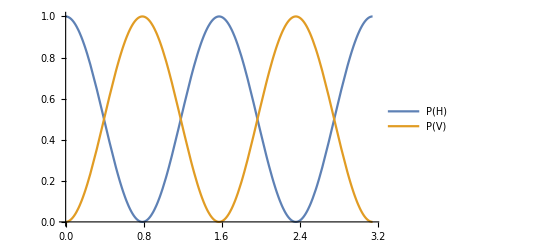

```mathematica
H = xi/.{α->0,β->0};
(*check: rotating the half wave plate an angle 45 degrees (π/4) should rotate the linear polarization by 2*45=90 degrees (π/2). It does.*)
Plot[Evaluate[(hwp[β].H)^2],{β,0,π},PlotLegends->{"P(H)","P(V)"}]
```

```mathematica
Abs[5Exp[-ⅈ 5]]
```

5

```mathematica
BlochVector[jonesVec_]:={Cos[Arg[jonesVec[[2]]]]Sin[2ArcCos[jonesVec[[1]]]],Sin[Arg[jonesVec[[2]]]]Sin[2ArcCos[jonesVec[[1]]]],Cos[2ArcCos[jonesVec[[1]]]]};
```

```mathematica
BlochVector[{1,0}]
```

{0,0,1}

```mathematica
Show[blochSphere,ParametricPlot3D[BlochVector[hwp[β].H],{β,0,π/4},Boxed->False],PlotLabel-> "Rotating a HWP through angle π/4",ImageSize->Medium]
```

-Graphics3D-

```mathematica
Show[blochSphere,ParametricPlot3D[BlochVector[qwp[β].H],{β,0,π/4},Boxed->False],PlotLabel-> "Rotating a QWP through angle π/4"]
```

-Graphics3D-

```mathematica
BlochVector[qwp[#].H]&/@{0,π/8,π/4}//N
```

{{0.,0.,1.},{0.747273+0.138575 ⅈ,0.747273+0.138575 ⅈ,0.414214-0.5 ⅈ},{0.899454-0.555893 ⅈ,0.899454-0.555893 ⅈ,-1.-1. ⅈ}}

```mathematica
blockvecs =BlochVector[qwp[#].H*conj[(qwp[#].H)[[1]]]]&/@{0,π/8,π/4}//N
```

{{0.,0.,1.},{0.572822+0. ⅈ,0.810093+0. ⅈ,0.125+0. ⅈ},{1.83697×10^-16-1.11803 ⅈ,0.,-1.5-1.3692×10^-16 ⅈ}}

```mathematica
qwp[β].H*conj[(qwp[β].H)[[1]]]//FullSimplify
```

{Cos[β]^4+Sin[β]^4,1/2 (ⅈ+Cos[2 β]) Sin[2 β]}

## Bloch Vectors on a Bloch Sphere

a nice derivation of the transformation of the Jones vectors and operators to the Bloch sphere picture is given in David Nadlinger’s Masters thesis. below are the results.

```mathematica
waveplate[α_,β_]:=({{Cos[α/2]^2-Cos[4β] Sin[α/2]^2, Cos[2β]Sin[α], Sin[4β] Sin[α/2]^2}, {-Cos[2β]Sin[α], Cos[α], Sin[2β]Sin[α]}, {Sin[4β] Sin[α/2]^2, -Sin[2β]Sin[α], Cos[α/2]^2+Cos[4β] Sin[α/2]^2}});(*α = retardance [rad], real space angle of waveplate coordinate rotation [rad]*)
hwp[β_]:=waveplate[π,β];
qwp[β_]:=waveplate[π/2,β];
h = {0,0,1};
v={0,0,-1};
d={1,0,0};
a={-1,0,0};
l={0,-1,0};
r={0,1,0};
```

```mathematica
Show[blochSphere,ParametricPlot3D[hwp[β].h,{β,0,π/4},Boxed->False],PlotLabel-> "Rotating a HWP through angle π/4",ImageSize->Medium]
Show[blochSphere,ParametricPlot3D[qwp[β].h,{β,0,π/4},Boxed->False],PlotLabel-> "Rotating a QWP through angle π/4",ImageSize->Medium]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[blochSphere,ParametricPlot3D[{qwp[β].d,hwp[β].d},{β,0,π},Boxed->False,PlotLegends-> {"QWP","HWP"}],ImageSize->Medium]
```

-Graphics3D-